# Задача 1

Уравнение Шредингера на радиальную часть волновой функции электрона в атоме водорода имеет вид:
u''  +   2/ru− (l(l+1))/r^2u=-ϵ u
Здесь R = u/r

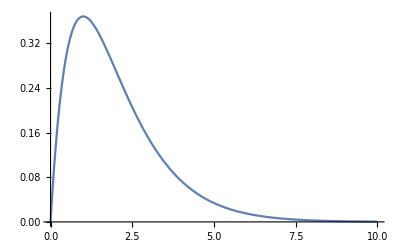

```mathematica
r1 = 10;
l = 0;
EE =-1;
solution = NDSolve[{r^2 uu''[r] + 2r uu[r]- l(l+1)uu[r] == -EE r^2 uu[r], uu'[10^-8]==1,uu[10^-8] == 0}, uu, {r, 10^-8, r1}][[1]];
Plot[uu[r]/.solution,{r,10^-8,r1}]
```

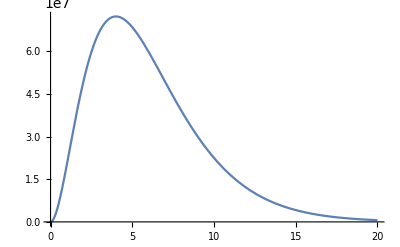

```mathematica
EE =-1/4;
r1 = 20;
l=1;
solution = NDSolve[{r^2 uu''[r] + 2r uu[r]- l(l+1)uu[r] == -EE r^2 uu[r], uu'[10^-8]==1,uu[10^-8] == 0}, uu, {r, 10^-8, r1}][[1]];
Plot[uu[r]/.solution,{r,10^-8,r1}]
```

# Задача 2

```mathematica
q/:
q^(m_):=-1*q^(m-2)/;m≥2
??q
```

```mathematica
q^2+2q^4+q^3
```

1-q

# Задача 3*

```mathematica
i /:
i^2:= -1
j /:
j^2:= -1
k /:
k^2:= -1
i j ^:= k
j k ^:= i
k i ^:= j
```

```mathematica
??i
```

# Задача 4

```mathematica
HamiltonEq[H_,coord_]:=
Block[{n,i,equations},
n=Length[coord];
equations=Table[0,n];
For[i=1,i≤ n,i++,
equations[[i]]={
D[coord[[i,2]][t],t]==-D[H,coord[[i,1]][t]],
D[coord[[i,1]][t],t]==D[H,coord[[i,2]][t]]
};
];
Return[equations]
];
```

```mathematica
H1=1/(2m)*p[t]^2+U[q[t]];
H2=1/(2m[1])*p[1][t]^2+1/(2m[2])*p[2][t]^2+U[q[1][t]];
HamiltonEq[H1,{{q,p}}]//TableForm
```

p'[t]==-U'[q[t]] | q'[t]==p[t]/m

```mathematica
HamiltonEq[H2,{{q[1],p[1]},{q[2],p[2]}}]//TableForm
```

p[1]'[t]==-U'[q[1][t]] | q[1]'[t]==(p[1][t])/m[1]
p[2]'[t]==0 | q[2]'[t]==(p[2][t])/m[2]